# Kompleksna analiza

1. Poiščite u(x,y)=realni del in v(x,y)=imaginarni del funkcije w=f(z), če je z=x+iy, w=u+iv in f(z) = z^2e^z !
    
Rezultat:
u = ⅇ^x x^2 Cos[y]-ⅇ^x y^2 Cos[y]-2 ⅇ^x x y Sin[y]
v = 2 ⅇ^x x y Cos[y]+ⅇ^x x^2 Sin[y]-ⅇ^x y^2 Sin[y]

```mathematica
?Re
?Im
?ComplexExpand
```

```mathematica
Re[2 + 5  I]
Im [2+ 5 I]
(1+I) *(3 - I)
ComplexExpand[%]

(1+I)^I
ComplexExpand[%]
```

2

5

4+2 ⅈ

4+2 ⅈ

(1+ⅈ)^ⅈ

ⅇ^(-π/4) Cos[Log[2]/2]+ⅈ ⅇ^(-π/4) Sin[Log[2]/2]

```mathematica
f[z_]:=z^2 Exp[z]
z=x+I y


Re[f[z]] (*ne ve da sta x realen in y kopleksen*)
Im[f[z]]
ComplexExpand[f[z]] (*to ni ok*)


(*Samo ta vrstni red je ok*)
u=ComplexExpand[Re[f[z]]] (*razširi in ve da sta x in y realni*)
v=ComplexExpand[Im[f[z]]]
```

x+ⅈ y

Re[ⅇ^(x+ⅈ y) (x+ⅈ y)^2]

Im[ⅇ^(x+ⅈ y) (x+ⅈ y)^2]

ⅇ^x x^2 Cos[y]-ⅇ^x y^2 Cos[y]-2 ⅇ^x x y Sin[y]+ⅈ (2 ⅇ^x x y Cos[y]+ⅇ^x x^2 Sin[y]-ⅇ^x y^2 Sin[y])

ⅇ^x x^2 Cos[y]-ⅇ^x y^2 Cos[y]-2 ⅇ^x x y Sin[y]

2 ⅇ^x x y Cos[y]+ⅇ^x x^2 Sin[y]-ⅇ^x y^2 Sin[y]

2. Izračunajte približno vrednost (3+i)^(2-i). 
     Sugestija: Uporabite funkcijo ComplexExpand za natančen in N za približen izračun.
    
Rezultat: 12.0547-6.708 ⅈ

```mathematica
z=(3 + I)^(2-I)
ComplexExpand[z] //N
N[z]
```

(3+ⅈ)^(2-ⅈ)

12.0547-6.708 ⅈ

12.0547-6.708 ⅈ

3. Poiščite vsaj eno rešitev enačbe Sin[z]=3.
     Rešitev zapišite v obliki x+iy, kjer sta x in y realna.
    
Rezultat: π/2-ⅈ Log[3+2 √2]

```mathematica
Clear[z]
Solve[Sin[z]==3]//ComplexExpand
```

{{z→ConditionalExpression[π/2+2 π C[1]+ⅈ Log[3+2 √2],C[1]∈ℤ]},{z→ConditionalExpression[π/2+2 π C[1]-ⅈ Log[3+2 √2],C[1]∈ℤ]}}

4.  Z dano sekvenca ukazov preverite Cauchy-Riemannov sistem enačb za eksponetno funkcijo.
     Zamenjajte  f[z]=Exp[z] z vsako od naslednjih funkcij: sin(z̄), z^3, iz-2(z̄)^3, tan(z^3).
     Katere od navedenih funkcij so analitične ?
     
Rezultat:
e^z			da
sin(z̄)		ne
z^3			da
iz-2(z̄)^3		ne
tan(z^3)		da

```mathematica
Clear[x,y,z,u,v,f];
z=x+I y;

f[z_]:=Exp[z]
u=ComplexExpand[Re[f[z]]]
v=ComplexExpand[Im[f[z]]]
Simplify[D[u,x]-D[v,y]]
Simplify[D[u,y]+D[v,x]]


f[z_]:=Sin[Conjugate[z]]
u=ComplexExpand[Re[f[z]]]
v=ComplexExpand[Im[f[z]]]
Simplify[D[u,x]-D[v,y]]
Simplify[D[u,y]+D[v,x]]

f[z_]:=z^3
u=ComplexExpand[Re[f[z]]]
v=ComplexExpand[Im[f[z]]]
Simplify[D[u,x]-D[v,y]]
Simplify[D[u,y]+D[v,x]]
```

ⅇ^x Cos[y]

ⅇ^x Sin[y]

0

0

Cosh[y] Sin[x]

-Cos[x] Sinh[y]

2 Cos[x] Cosh[y]

2 Sin[x] Sinh[y]

x^3-3 x y^2

3 x^2 y-y^3

0

0

5. Dana je funkcija u(x,y)= x-3 x^2+4 x^3+3 y^2-12 x y^2.
     Določite funkcijo v(x,y) tako, da je funkcija f(z) = u(x,y) + i v(x,y) analitična in f(0)=0, kjer je  z=x+iy.
     Koliko je v(1,1) ?
    
Rezultat: 3

```mathematica
u=x-3x^2+4x^3+3y^2-12x y^2

(*Test ali sploh obstaja*)
D[u,x,x]+D[u,y,y]

Integrate[D[u,x], y]
Integrate[-D[u,y],x]
(*Vzamemo vse člene ki se pojavijo vsaj v enem + k*)
v=y-6 x y+12 x^2 y-4 y^3 + k
Solve[{v/.{x-> 0,y-> 0}}==0, k] //Flatten (*damo oklepaje stran*)

v/.% /.{x->1,y->1}
```

x-3 x^2+4 x^3+3 y^2-12 x y^2

0

y-6 x y+12 x^2 y-4 y^3

-6 x y+12 x^2 y

k+y-6 x y+12 x^2 y-4 y^3

{k→0}

3

6. Poiščite konvergenčno območje vrste
     	∑_(n=1)^∞ ((1+i)/(z-4+3i))^n + ∑_(n=0)^∞ ((z-4+3i)/3)^n
     Razlaga: Konvergenčni radij potenčne vrste ∑_(n=0)^∞ C_n z^n se izračuna z limito zaporedja R=lim|C_n/C_(n+1)| , za kar je ukaz Limit. Konvergiralo je sam kjer je |z-z0| bilo manj kot radij.
    
Rezultat: √2 < |z-4+3i| < 3
Opomba: Rezultat se da prikazati tudi grafično, oglejte si rešitev!

```mathematica
?Limit
```

```mathematica
c[n_]:=(1+I)^n
Limit[Abs[c[n]/c[n+1]],n->Infinity]

c[n_]:=(1/3)^n
Limit[Abs[c[n]/c[n+1]],n->Infinity]
```

1/(√2)

3

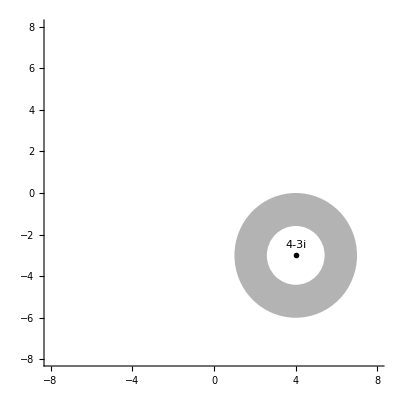

```mathematica
Show[
 Graphics[{
  { GrayLevel[0.7], Disk[{4,-3},3] },
  { GrayLevel[1], Disk[{4,-3},Sqrt[2]] },
  { PointSize[0.01], Point[{4,-3}] },
  Text["4-3i",{4,-2.5}]
  }],
 Axes->True,AspectRatio->Automatic,PlotRange->{{-8,8},{-8,8}}
 ]
```

7. (Integral kompleksne funkcije kot krivuljni integral 2. vrste)
     Izračunajte integrale ∫_C F(z)ⅆz za vse kombinacije danih krivulj C in funkcij F(z):
     C_1:  spirala    r=φ/(2π)
C_2:  parabola   y=x-x^2
F_1(z)=z^2   - je analitična, pričakujemo enak rezultat
F_2(z)=(z̄)^2
     od začetne točke z_1=0 do točke z_2=1.

Rezultati: IC1F1 = IC2F1 = 1/3, IC1F2 =(2+2 ⅈ π-π^2)/π^2, IC2F2 =4/15-ⅈ/3

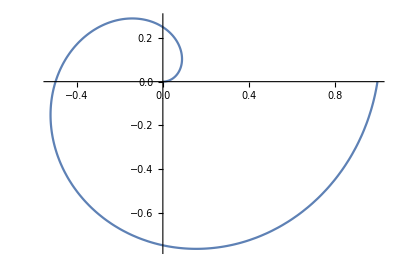

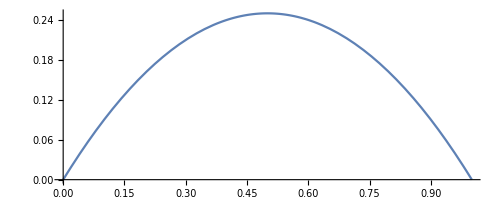

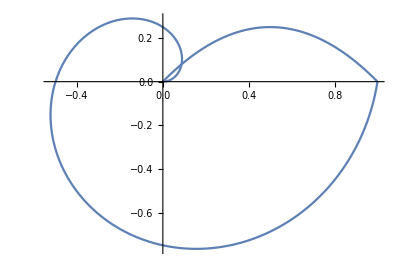

```mathematica
C1=ParametricPlot[{φ Cos[φ]/(2π),φ Sin[φ]/(2π)},{φ,0,2π}]
C2=ParametricPlot[{x,x(1-x)},{x,0,1}]
Show[C1,C2,AspectRatio->Automatic]
```

```mathematica
F1[z_]:=z^2;
F2[z_]:=ComplexExpand[Conjugate[z^2]];

z1=φ( Cos[φ]+I  Sin[φ])/(2π); (*parametrizacija krivulje*)
z2=x+I x(1-x);

IC1F1=Integrate[F1[z1] D[z1,φ], {φ,0,2Pi}] (*v funkcijo vstavimo parametrizacijo in množimo z odvodom parametrizacije*)
IC2F1=Integrate[F1[z2] D[z2,x], {x,0,1}] 
IC1F2=Integrate[F2[z1] D[z1,φ], {φ,0,2Pi}] 
IC2F2=Integrate[F2[z2] D[z2,x], {x,0,1}] 

Clear[z]
Integrate[z^2,{z,0,1}] (*analitična in jo lahko kar normalno*)
```

1/3

1/3

-1+2/π^2+(2 ⅈ)/π

4/15-ⅈ/3

1/3

8. Cauchyjeva integralska formula:1/(2πⅈ)∫_C (f(z))/(z-z_0)ⅆz  = f(z_0) 
     Izračunajte integrala
     I_1= ∫_C z^2/(z-(7+6ⅈ))     in     I_2=∫_C z^2/(z-(9+6ⅈ)),
     kjer je krivulja C krožnica|z-6ⅈ|=8.

     Integrala izračunajte na dva načina
     1. Po definiciji kot krivuljni integral 2.vrste
     2.  Z uporabo Cauchyjeve integralske formule
     in primerjajte rezultate. 

     Za preglednost razmer glejte izdelano sliko.

Rezultata: I_1=(-168+26 ⅈ) π, I_2= 0

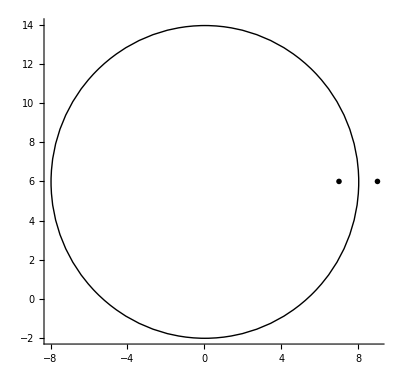

```mathematica
Show[
 Graphics[{
  Circle[{0,6},8],
  { PointSize[0.01], Point[{7,6}] },
  { PointSize[0.01], Point[{9,6}] }
  }],
 
 Axes->True,AspectRatio->Automatic
 ]
```

```mathematica
z01=7+6I
z02=9+6I
f[z_]:=z^2
f1[z_]:=f[z]/(z-z01)
f2[z_]:=f[z]/(z-z02)

z= 8E^(I t)+6I (*krožnice je najlažje z e na i fi parametrizirati - Radij krat e na ikrat patrameter + središče*)
Integrate[f1[z]* D[z,t], {t,0,2Pi}]
Integrate[f2[z]* D[z,t], {t,0,2Pi}]

2Pi I f[z01] (*po cauchiju f je števec*)
```

7+6 ⅈ

9+6 ⅈ

6 ⅈ+8 ⅇ^(ⅈ t)

(-168+26 ⅈ) π

0

(-168+26 ⅈ) π

9. Poiščite glavni del Laurentove vrste dane funkcije f(z) v okolici točke z_0, če je
     a) f(z)= (sin z)/z^3  ,  z_0=0
     b) f(z)= (cos( z-ⅈ))/((z^2+1)^2)  ,  z_0=ⅈ
     
Rezultata:
a) 1/z^2
b) -1/(4 (z-ⅈ)^2)-ⅈ/(4 (z-ⅈ))

```mathematica
?Series
?Normal
```

```mathematica
Clear[z]
f1=Sin[z]/z^3
f2=Cos[z-I]/(z^2+1)^2

Series[f1,{z, 0, -1}]
Normal[Series[f1,{z, 0, -1}]] (*Ali //N poreže ostanek)*)
Normal[Series[f2,{z, I, -1}]]
```

Sin[z]/z^3

Cosh[1+ⅈ z]/((1+z^2)^2)

1/z^2+O[z]^0

1/z^2

-1/(4 (-ⅈ+z)^2)-ⅈ/(4 (-ⅈ+z))

10. Dana je funkcija f(z)=(z^3-2 z^2+z)/(cos πz/2)^5 .
     Izračunajte Residuum funkcije f(z) v točki z=1 na vse tri načine:
     a)  Razvijte f(z) v Laurentovo vrsto v okolici z=1 z ukazom Series
     b)  Ugotovite stopnjo pola, uporabi formulo za residuum in ukaz Limit -> faktor, neke stopnje zgoraj neke spodaj.
     c)  Uporabite ukaz Residue
     ter primerjajte rezultate!

Rezultat: -20/(3 π^3)

```mathematica
?Residue
```

```mathematica
f=(z^3-2z^2+z)/Cos[Pi z/2]^5
Residue[f,{z,1}]
```

(z-2 z^2+z^3) Sec[(π z)/2]^5

-20/(3 π^3)

# Dodatni nalogi

1. Izračunajte integral  ∫_(|z-π/2+i|=2) 1/(cos(z)-(5i)/12)dz, kjer je integracija v pozitivni smeri. UPORABA RESIUMOV.
     Namig: izrek o residuih.

Rezultat: -(24 π i)/13

2. Izračunajte integrala  ∫_(-∞)^∞ 1/((x^2+4)^2(x^2+9)^2)dx  in  ∫_0^∞ x^2/((x^2+4)^2)dx na dva načina in v vsakem od integralov primerjajte rezultata za oba načina (a in b)! UPORADA RESIDUOV ZA REALNE.
     a) Uporabite ukaz Integrate za določeni integral
     b) Uporabite izrek o residuih in ukaz Residue

Rezultata:  (31 π)/54000, π/8